```mathematica
Check if pdb chain looks like smth from the GPCRdb table, if yes - assign subfamily to it, else - generate list to check manually later
```

```mathematica
pathToProject="/media/my_extra_space/projects/1510GPCR/";
pathToDump=pathToProject<>"dumps/";
Get[pathToDump<>"fromDeterminingChainsForPrimaryLabeling.m"];
```

```mathematica
Initialize alignment table
```

```mathematica
pathToTable=pathToProject<>"inputs/tables/";
alignmentTable=Import[pathToTable<>"residues_alignment_rho.csv"];

initAlignmentTables[nhel_,nfam_]:=Module[{i,inneralignmentTables},(inneralignmentTables=Range[1,nhel];
Do[inneralignmentTables[[i]]=Select[alignmentTable,ToExpression[StringTake[StringJoin[{#[[1]]," "}],1]]==i&];,{i,1,nhel}];
Return[inneralignmentTables];);];
dissectSeq[x_]:=StringJoin[StringReplace[x,{"1"->"","2"->"","3"->"","4"->"","5"->"","6"->"","7"->"","8"->"","9"->"","0"->""}]];

families=Drop[Drop[alignmentTable[[2]],1],-1];
numOfHelises=7;
numOfFamilies=Length[families];
alignmentTables=initAlignmentTables[numOfHelises,numOfFamilies];
helixGroupArray=Range[numOfHelises];
helixStringArray=Range[numOfHelises];
Do[helixGroupArray[[i]]=Range[numOfFamilies];
helixStringArray[[i]]=Range[numOfFamilies];,{i,1,numOfHelises}];
Do[s=alignmentTables[[i]];
s=sᵀ[[{1,j+1}]];
s=sᵀ;
s=Select[s,#[[2]]≠"-"&];
helixGroupArray[[i]][[j]]=sᵀ;
helixStringArray[[i]][[j]]=dissectSeq[sᵀ[[2]]];,{i,1,numOfHelises},{j,1,numOfFamilies}];

numOfFiles=Length@pdbsToChain;
```

```mathematica
Assess the longest intersection of GPCRdb table column and actual structure sequence, study the histogram
```

```mathematica
foundFamilies=(ConstantArray[{},numOfHelises])&/@pdbsToChain;
familyScores={};
unassigned={};
Module[{listOfSeqs,max,min,ss,nums,lostOrNot,newSeq,pos,curSeq},
listOfSeqs=pdbsToChainᵀ[[2]];
Do[ss=listOfSeqs[[i]];
max=Max[ssᵀ[[1]]];
min=Min[ssᵀ[[1]]];
nums=Range[min,max];
lostOrNot=Map[Intersection[ssᵀ[[1]],{#}]≠{}&,nums];
newSeq=Range[min,max];
Do[If[lostOrNot[[k-min+1]]==True,pos=(Flatten@Position[ssᵀ[[1]],k])[[1]];
newSeq[[k-min+1]]={k,ssᵀ[[2]][[pos]]};,newSeq[[k-min+1]]={k,"0"};];,{k,min,max}];
listOfSeqs[[i]]=newSeq;
pdbsToChain[[i]][[2]]=newSeq;
,{i,1,numOfFiles}];

Do[
curSeq=StringJoin[listOfSeqs[[n]]ᵀ[[2]]];
ss=ConstantArray[0,numOfFamilies];
Do[ss=ss+(StringLength[LongestCommonSubsequence[#1,StringJoin@(listOfSeqs[[n]]ᵀ[[2]])]]&/@helixStringArray[[i]]);,{i,1,numOfHelises}];
AppendTo[familyScores,ss];,{n,1,numOfFiles}];
];
```

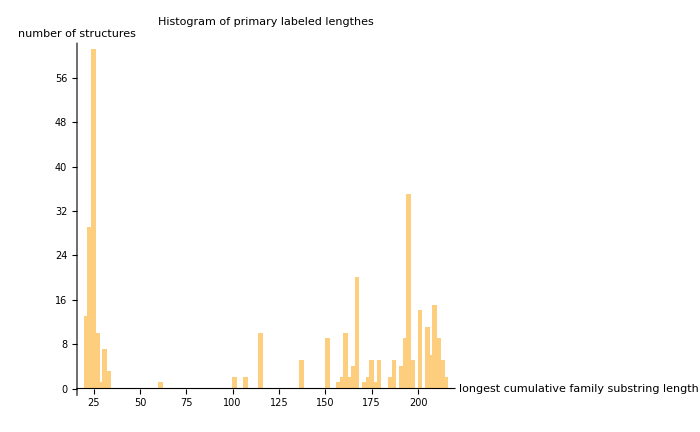

```mathematica
Histogram[Max[#]&/@familyScores,100,PlotRange->All, PlotLabel->Style["Histogram of primary labeled lengthes",Black],AxesLabel->{"longest cumulative family substring length","number of structures"},ImageSize->700]
```

```mathematica
Divide ids into two groups based on histogram: supposed rubbish and supposed structures from subfamilies present in GPCRdb table
```

```mathematica
minLabel=80;
assigned={};
Do[If[Max[familyScores[[i]]]<minLabel,AppendTo[unassigned,pdbsToChain[[i]]],AppendTo[assigned,{pdbsToChain[[i]],Position[familyScores[[i]],Max@familyScores[[i]]][[1]][[1]]}]];,{i,1,numOfFiles}];
```

```mathematica
Export list of unassigned pdbs for manual sieve (7tm or not 7tm);  and export lists as inputs for stride script
```

```mathematica
pathToDatFiles=pathToProject<>"datFiles/";
Export[pathToDatFiles<>"unassignedPdbs.dat",(ToUpperCase[unassignedᵀ[[1]]ᵀ[[1]][[#]]]<>"_"<>unassignedᵀ[[1]]ᵀ[[2]][[#]])&/@Range[Length@unassigned]];

Export[pathToDatFiles<>"assignedPdbsToStride.dat",(ToUpperCase[assigned[[#]][[1]][[1]][[1]]]<>"_"<>assigned[[#]][[1]][[1]][[2]])&/@Range[Length@assigned]];
```

```mathematica
Save[pathToDump<>"fromPrimaryLabelingForFurtherLabeling.m",{assigned,unassigned, helixGroupArray, helixStringArray, families,numOfHelises}];
```

```mathematica
assigned[[1]][[1]][[1]]
```

{1f88,A,CRYSTAL STRUCTURE OF BOVINE RHODOPSIN,X-RAY DIFFRACTION,2.80}